Load approximation package

```mathematica
Needs["FunctionApproximations`"]
```

We want to approximate the function Δ(a) = log a! - log √(2 π a)(a/e)^a for a>8

Note then that the Stirling series is given by Δ(a) = Σ_(n=0)c_n a^(1-2n) . To accurately approximate this function define t=1/a^2  and find the minimax approximation in terms of t on some pre-defined interval.

```mathematica
Δ[a_]:=LogGamma[a]-(a-1/2)Log[a] -1/2Log[2*Pi] + a;
```

Define F(t) = a Δ(a)=Δ(1/√t)/√t which has the series expansion F(t) = Σ_(n=0)c_n t^n

```mathematica
F[t_]:=Δ[1/Sqrt[t]]/Sqrt[t];
```

It can be hard to work with the exact form of F due to the removable pole at t=0. Instead consider the series expansion around t=0 up to arbitrary order.

```mathematica
Z[t_,n_]:=Normal[Series[F[t],{t,0,n}]]
```

Now consider a rational minimax approximation of order (p,q) of the function R_m(t) = F(t)  -Σ_(n=0)^m t^n c_n , i.e. the remainder of the truncated Stirling series.

```mathematica
m = 0;
p = 0;
q = 0;
tmax = 1/20^2;
tmin = 1/80^2;
minimax=MiniMaxApproximation[(F[t] - Z[t,m])/(t^(m+1)),{t,{tmin,tmax},p,q},MaxIterations->100,WorkingPrecision->400][[2]];
poly[t_]:=Evaluate[ Z[t,m]+t^(m+1)minimax[[1]]]
N[minimax[[2]],5] (* minimax error *)
```

First::nofirst: FunctionApproximations`Private`dummy[] has zero length and no first element.

Part::partw: Part 1 of {} does not exist.

First::nofirst: FunctionApproximations`Private`dummy[] has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

0.00033428

Define relative error of the minimax approximation to the original function and plot over range of allowed values to check whether it is of machine precision level

```mathematica
prec = $MachineEpsilon/2; (*double precision*)
prec = 2^-24;(*single precision*)
```

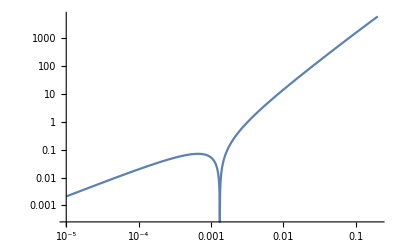

```mathematica
rerr[t_]:=Abs[1-poly[t]/F[t]]
LogLogPlot[rerr[t]/prec,{t,10^-5,tmax + 2/10},WorkingPrecision->400,PlotRange->All,GridLines->{{tmax},{1}},GridLinesStyle->Directive[Red,Thick]]
```

Check how the approximation performs in the overall approximation of Δ(a)

```mathematica
r[x_]:=x^-2;
P[x_]:=poly[r[x]]/x;
```

Over what range of x is the approximation valid?

```mathematica
X={1/Sqrt[tmax],1/Sqrt[tmin]}
```

{20,80}

Red line indicates relative precision at machine precision level

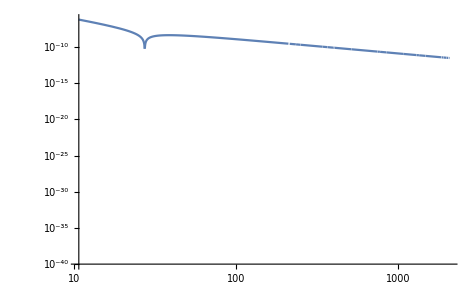

```mathematica
LogLogPlot[Abs[1-P[x]/Δ[x]],{x,X[[1]]-10,X[[2]]+2000},PlotRange->{All,{10^-40,10*prec}},WorkingPrecision->400,GridLines->{{X[[1]],X[[2]]},{prec}},GridLinesStyle->Directive[Red,Thick]]
```

Finally print out the approximation

```mathematica
N[poly[t],8]
```

0.083333333-0.0027767253 t